{6.26056,6.36437,7.20946,5.6919,6.34509,4.98162,6.27469,5.88057,9985,7.03757,5.6932,6.35931,6.52531,5.71421,6.54456,6.86171}
 |  |  |  |

9.27643

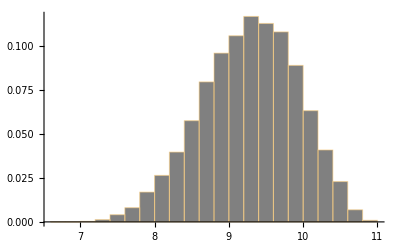

```mathematica
dist=BetaDistribution[2,1.5];
LMax[l1_,l2_]:=Max/@Transpose[{l1,l2}];
RV[lo_,hi_]:=lo+(hi-lo)RandomVariate[dist,10^4];
D1=RV[2,4];
D2=RV[4,7];
D3=RV[2,4];D4=RV[2,3];D5=RV[2,3];
S2=D1;
S3=D1;
S4=S3+D3;
S5=S3+D3
H[V_]:=Histogram[V,Automatic,"Probability",ChartStyle->{Gray}];
Cmax=LMax[LMax[S2+D2,S4+D4],S5+D5];
Mean[Cmax]
H[Cmax]
```

```mathematica
Export["/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/cmax.eps",%231,"EPS"]
```

/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/cmax.eps

```mathematica
Export["/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/cmax.eps",%131,"EPS"]
```

/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/cmax.eps

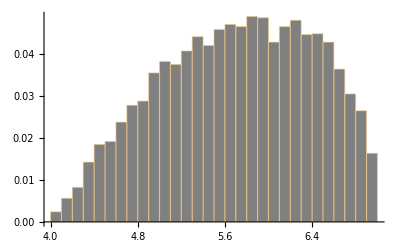

```mathematica
H[D2]
```

```mathematica
Export["/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/D2.eps",%234,"EPS"]
```

/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/D2.eps

```mathematica
Export["/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/D2.eps",%133,"EPS"]
```

/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/D2.eps